```mathematica
(*market parameters*)
SpotMax=70;(*stock price bound*)
SpotMin=0;(*stock price bound*)
K=40;(*strike price*)
r=.1;(*risk-free rate*)
σ=.2;(*volatility*)
T=100;(*termination*)
(*model parameters*)
Δt=1;(*time step (mesh time parameter)*)
h=30; (*mesh spatial parameter*)
elements=ConstantArray[0,h];(*List of endpoints for elements*)
For[i=1,i≤h,i++,
elements[[i]]={(i-1)(SpotMax-SpotMin)/h,i(SpotMax-SpotMin)/h}]
```

```mathematica
(*Lagrange polynomials for interpolation*)
L[x_,α_,β_] := {(β-x)/(β-α),(x-α)/(β-α)}
```

```mathematica
(*Matrix initialization*)
Kij=ConstantArray[0,{h+1,h+1}];
Mij=ConstantArray[0,{h+1,h+1}];
For[elt=1,elt≤h,elt++,
α=elements[[elt]][[1]];
β=elements[[elt]][[2]];
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
(*Integration by parts on dV/dt-1/2(d^2 V)/dS^2*)
Kij[[elt+i-1,elt+j-1]]+=Integrate[D[L[x,α,β][[i]],x]*D[L[x,α,β][[j]],x],{x,α,β}];
Mij[[elt+i-1,elt+j-1]]+=Integrate[L[x,α,β][[i]]*L[x,α,β][[j]],{x,α,β}];
];
];
];
Dij=Mij-Δt/2 Kij;
(*fix spatial endpoints*)
Mij[[1]]=ConstantArray[0,h+1];
Mij[[1,1]]=1;
Dij[[1]]=ConstantArray[0,h+1];
Dij[[1,1]]=1;
Mij[[h+1]]=ConstantArray[0,h+1];
Mij[[h+1,h+1]]=1;
Dij[[h+1]]=ConstantArray[0,h+1];
Dij[[h+1,h+1]]=1;
```

```mathematica
(*Initial value: price at termination*)
(*a is the price vs. stock price data*)
a=ConstantArray[0,h+1];
a[[1]]=0;
For[i=2,i≤h,i++,
(*value at termination: option exercised or not exercised*)
If[elements[[i]][[1]]>K,a[[i]]=elements[[i]][[1]]-K];
];
a[[h+1]]=SpotMax-K;
```

```mathematica
(*Creating output data*)
B=Inverse[Mij].Dij;
TimeLength=IntegerPart[T/Δt];
(*Output matrix for all the time slices*)
Output=ConstantArray[0,TimeLength];
Output[[1]]=a;
For[t=1,t≤TimeLength-1,t++,
Output[[t+1]]=B.Output[[t]];
For[i=1,i≤Length[Output[[t+1]]],i++,
(*Cleaning up artifacts*)
If[Output[[t+1,i]]<0,Output[[t+1,i]]=0];
];
];
```

```mathematica
(*Graphics postprocessing*)
Points=ConstantArray[0,{TimeLength*(h+1),3}];
k=1;
For[i=0,i≤TimeLength-1,i++,
For[j=0,j≤h,j++,
Points[[k]]={T-i*Δt,j*((SpotMax-SpotMin)/h),Output[[i+1,j+1]]};
k++;
];
];
ListPlot3D[Points,ColorFunction->Function[{x,y,z},Hue[.15(y-3.5)]],ImageSize->Large]
```

-Graphics3D-

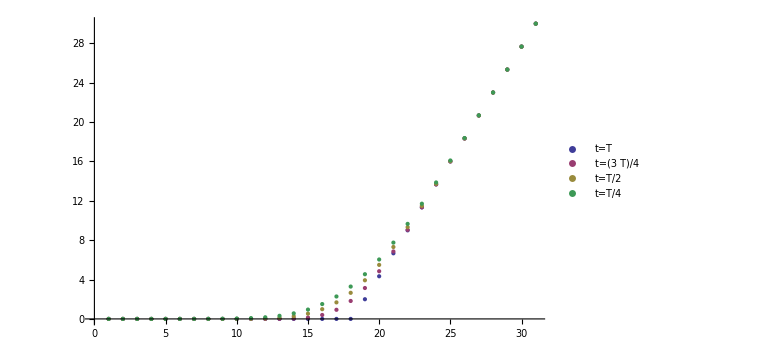

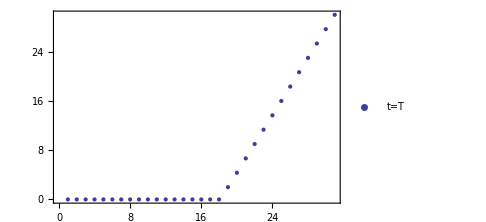
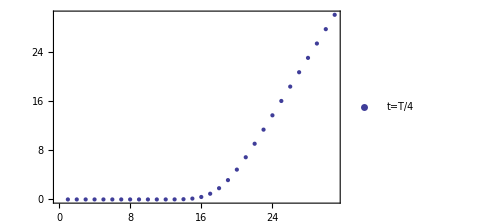
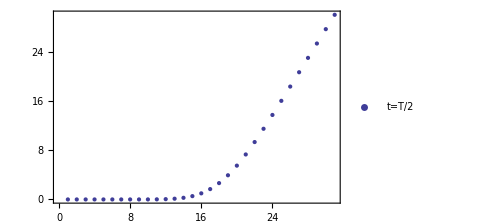
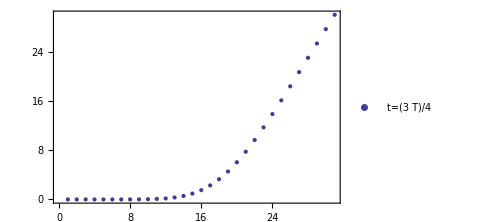
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
ListPlot[{Output[[1]],Output[[IntegerPart[T/4]]],Output[[IntegerPart[T/2]]],Output[[IntegerPart[(3T)/4]]]},PlotLegends->{"t=T","t=(3  T)/4","t=T/2","t=T/4"},ImageSize->Large]
Grid[{{ListPlot[Output[[1]],PlotLegends->{"t=T"},Frame->True,ImageSize->Medium],ListPlot[Output[[T/4]],PlotLegends->{"t=T/4"},Frame->True,ImageSize->Medium]},{ListPlot[Output[[T/2]],PlotLegends->{"t=T/2"},Frame->True,ImageSize->Medium],ListPlot[Output[[(3T)/4]],PlotLegends->{"t=(3  T)/4"},Frame->True,ImageSize->Medium]}},Frame->All,Spacings->{0,0}]
```